```mathematica
ClearAll["Global`*"];Clear[Derivative];
```

```mathematica
Import[NotebookDirectory[]<>"lattice.wl"];
```

```mathematica
L=4;
d=4;
```

```mathematica
lattice=getLattice[L,d];
```

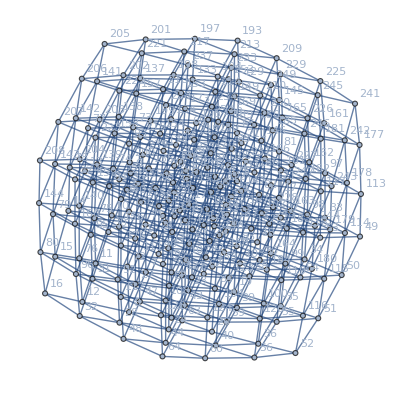

```mathematica
lattice=Fold[SetProperty[{#1,#2},VertexLabels->#2]&,lattice,VertexList[lattice]]

lattice=Fold[SetProperty[{#1,#2},EdgeLabels->PropertyValue[{#1,#2},EdgeCapacity]]&,lattice,EdgeList[lattice]];
```

```mathematica
(*Function to map Plaquettes as lists of edges *)
plaquetteOfVertexInPlane[i_,plane_,L_]:=
Fold[If[#1=={},
Append[#1,{i,nextVertex[i,#2,L]}],
If[NumericQ[Last[Last[#1]]],
Append[#1,{Last[Last[#1]],
If[Length[#1]<2,
nextVertex[Last[Last[#1]],#2,L],
previousVertex[Last[Last[#1]],#2,L]
]}
],Append[#1,{Last[Last[#1]],False}]]
]&,{},Join[plane,plane]]
```

```mathematica
isPlaquette[plaquette_]:=Fold[If[#1==True&&NumericQ[First[#2]]&&NumericQ[Last[#2]],True,False]&,True,plaquette]
```

```mathematica
getInternalPlaquettes[L_,d_]:=Select[Sort[Flatten[Map[Function[vl,plaquetteOfVertexInPlane[vl,#,L]&/@Subsets[Range[1,d],{2}]][#]&,Range[1,L^d]],1]],isPlaquette];
```

```mathematica
plaqs= getInternalPlaquettes[L,d]
```

{{{1,2},{2,6},{6,5},{5,1}},{{1,2},{2,18},{18,17},{17,1}},{{1,2},{2,66},{66,65},{65,1}},{{1,5},{5,21},{21,17},{17,1}},{{1,5},{5,69},{69,65},{65,1}},{{1,17},{17,81},{81,65},{65,1}},853,{{246,247},{247,251},{251,250},{250,246}},{{247,248},{248,252},{252,251},{251,247}},{{249,250},{250,254},{254,253},{253,249}},{{250,251},{251,255},{255,254},{254,250}},{{251,252},{252,256},{256,255},{255,251}}}
 |  |  |  |

```mathematica
(* todo test for all d *)
countTest[plaqs_,d_]:=
If[d==2,Length[plaqs]==(L-1)^d,If[d==3,2d(L-1)^d/2+2d*(L-1)^2/2,"no test yet"]]
```

```mathematica
countTest[plaqs,d]
```

no test yet